-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 13 IV.D The Ideal Gas

```mathematica
(*-------------------------------------*)
t1=TimeObject[{7,0,0}];
t2=TimeObject[{7,10,0}];
Lab1="Thermo.&Stat.\nGeneral Picture";
(*-------------------------------------*)
(*-------------------------------------*)
t3=TimeObject[{7,8,0}];
t4=TimeObject[{7,30,0}];
Lab2="Thermo.&Stat.\nMindMap Lecture";
(*-------------------------------------*)
(*-------------------------------------*)
t5=TimeObject[{8,2,0}];
t6=TimeObject[{8,20,0}];
Lab3="Thermo.&Stat.\nStudents talks";
(*-------------------------------------*)
(*-------------------------------------*)
t71=TimeObject[{8,5,0}];
t81=TimeObject[{8,10,0}];
Lab41="Thermo.&Stat.\nBreak";
(*-------------------------------------*)
(*-------------------------------------*)
t7=TimeObject[{7,35,0}];
t8=TimeObject[{8,45,0}];
Lab4="Thermo.&Stat.\nSlides";
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
t72=TimeObject[{8,50,0}];
t82=TimeObject[{9,0,0}];
Lab42=Hyperlink[Style["Thermo.&Stat.\n   Questions?\n   &\n   Chat..."],"https://mmaitex-gemmini.fly.dev/"];

TS1=TimelinePlot[{
Interval[{t1,t2}]->Lab1,
Interval[{t3,t4}]->Lab2,
Interval[{t5,t6}]->Lab3,
Interval[{t71,t81}]->Lab41,
Interval[{t7,t8}]->Lab4,
Interval[{t72,t82}]->Lab42
},
Frame->True,
FrameStyle->Directive[Thickness[0.003],FontFamily->"Comic Sans MS", FontSize->28],
LabelStyle->Directive[FontFamily->"Comic Sans MS",Black,18],ImageSize->800,Background->LightBlue,AspectRatio->0.35
]
```

-Graphics-

## The ideal gas

```mathematica
(1) -- In our study of gases, we can think of each particle as having a position and momentum in space. For a gas with N particles, we need to keep track of all these positions and momenta, which we call micro-states. These micro-states are represented by points in a special space called phase space, which has 6N dimensions - three for position and three for momentum of each particle.

To simplify our analysis, we often ignore the potential energy from particle interactions. Instead, we focus on the kinetic energy of the particles, which is described by a function called the Hamiltonian. This Hamiltonian helps us understand how the system's energy changes as the particles move around.

By looking at these micro-states and using the Hamiltonian, we can start to build a picture of how the gas behaves on a microscopic level, which is crucial for understanding its macroscopic properties.
```

Statistical Mechanics
Ramirez (2)

```mathematica
MaTeX["\\mathcal{H}=\\sum_{i=1}^{N}\\left[\\frac{\\vec{p}_{i}^{2}}{2 m}+U\\left(\\vec{q}_{i}\\right)\\right]", Magnification -> 4]
```

-Graphics-

(3) -- Let's think about a box containing particles. The box has a volume V, and it creates a potential U(q) that affects the particles inside. 

When we describe a microcanonical ensemble, we need three key pieces of information: the total energy E, the volume V, and the number of particles N. We can represent this as M = (E, V, N).

For each possible arrangement of particles in the box (which we call a micro-state), there's a certain probability of it occurring. This probability is described by a joint probability density function.

By understanding these concepts, we can start to analyze how particles behave in confined spaces and predict the properties of large systems of particles.

Statistical Mechanics
Ramirez (4)

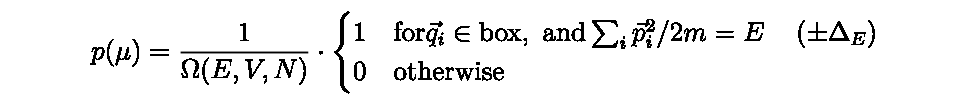

```mathematica
MaTeX["p(\\mu)=\\frac{1}{\\Omega(E, V, N)} \\cdot \\begin{cases}1 & \\text {for} \\vec{q}_{i} \\in \\text {box},~ \\text {and} \\sum_{i} \\vec{p}_{i}^{2} / 2 m=E \\quad\\left(\\pm \\Delta_{E}\\right) \\\\ 0 & \\text {otherwise}\\end{cases}", Magnification -> 4]
```

```mathematica
(5) -- In the allowed micro-states, coordinates of the particles must be within the box, while the momenta are constrained to the surface of the (hyper-) sphere $\sum_{i=1}^{N} \vec{p}_{i}^{2}=2 m E$. The allowed phase space is thus the product of a contribution $V^{N}$ from the coordinates, with the surface area of a $3 N$-dimensional sphere of radius $\sqrt{2 m E}$ from the momenta. (If the microstate energies are accepted in the energy interval $E \pm \Delta_{E}$, the corresponding volume in momentum space is that of a (hyper-)spherical shell of thickness $\Delta_{R}=\sqrt{2 m / E} \Delta E$.) The area of a $d$-dimensional sphere is $\mathcal{A}_{d}=S_{d} R^{d-1}$, where $S_{d}$ is the generalized solid angle.
```

(6) -- Let's think about a clever trick to find the solid angle in multiple dimensions. Imagine we have a bunch of Gaussian integrals - you know, those bell-shaped curves we see in statistics. If we multiply these integrals together, one for each dimension we're working in, we can actually use this to figure out the solid angle we're looking for. It's a neat way to tackle a complex problem using something more familiar from probability theory.

Statistical Mechanics
Ramirez (7)

```mathematica
MaTeX["I_{d} \\equiv\\left(\\int _{-\\infty}^{\\infty} e^{-x^{2}}\\right)^{d} \\,  d x=\\pi^{d / 2}", Magnification -> 4]
```

-Graphics-

```mathematica
(8) -- Alternatively, we may consider $I_{d}$ as an integral over an entire $d$-dimensional space, i.e.
```

Statistical Mechanics
Ramirez (9)

```mathematica
MaTeX["I_{d}=\\int  \\prod_{i \\,  d x_{i}=1}^{d} \\exp \\left(-x_{i}^{2}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
(10) -- Let's simplify our approach to this integral. Imagine we're looking at a sphere in multiple dimensions. Instead of dealing with separate coordinates, we can use a single variable R to represent the distance from the center. R.b2 is the sum of all our coordinate values squared.

When we make this change, we need to adjust our volume element. In these new coordinates, it becomes S_d R^(d-1) dR, where S_d is the surface area of a unit sphere in d dimensions, and d is the number of dimensions we're working in.

This transformation helps us handle spherically symmetric problems more easily, reducing a complex multidimensional integral to a simpler one-dimensional form.
```

Statistical Mechanics
Ramirez (11)

```mathematica
MaTeX["I_{d}=\\int _{0}^{\\infty} R^{d-1} e^{-R^{2}}  dR S_{d}=\\frac{S_{d}}{2} \\int _{0}^{\\infty} y^{d / 2-1} e^{-y} \\,  d y=\\frac{S_{d}}{2}(d / 2-1)!", Magnification -> 4]
```

-Graphics-

```mathematica
(12) -- where we have first made a change of variables to $y=R^{2}$, and then used the integral representation of $n$ !. Equating expressions (IV.28) and (IV.30) for $I_{d}$ gives the final result for the solid angle,
```

Statistical Mechanics
Ramirez (13)

```mathematica
MaTeX["S_{d}=\\frac{2 \\pi^{d / 2}}{(d / 2-1)!}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S_{d}=\\frac{2 \\pi^{d / 2}}{(d / 2-1)!}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S_d==(2 π^(d/2))/((d/2-1)!)

```mathematica
(14) -- In our exploration of phase space, we find that the volume available to our system is expressed as:

Ω = ∫∫...∫ dp₁...dpₙdq₁...dqₙ

This integral represents the sum of all possible microstates within our system. It spans across all momentum (p) and position (q) coordinates for each particle, from 1 to n. By calculating this volume, we gain insight into the system's entropy and the number of accessible states, which are fundamental to understanding its thermodynamic behavior.
```

Statistical Mechanics
Ramirez (15)

```mathematica
MaTeX["\\Omega(E, V, N)=V^{N} \\frac{2 \\pi^{3 N / 2}}{(3 N / 2-1)!}(2 m E)^{(3 N-1) / 2} \\Delta_{R}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Omega((Ener), V, N)=V^{N} \\frac{2 \\pi^{3 N / 2}}{(3 N / 2-1)!}(2 m (Ener))^{(3 N-1) / 2} \\Delta_{R}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Ω[Ener,V,N]==(V^N (2 π^((3 N)/2)) (2 m[Ener])^(1/2 (3 N-1)) Δ_R)/(((3 N)/2-1)!)

```mathematica
(16) -- When we're dealing with a large number of particles, we can calculate the entropy using a special mathematical trick. We take the natural logarithm of a complex expression that describes the system's arrangement. Then, we use something called Stirling's formula to simplify our calculation. 

In this process, we ignore some smaller terms because they don't matter much when we're working with really big numbers. These smaller terms are usually about the size of 1 or ln E (which is roughly the same as ln N when N is very large).

This approach helps us understand the behavior of systems with many particles, which is what we often encounter in thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (17)

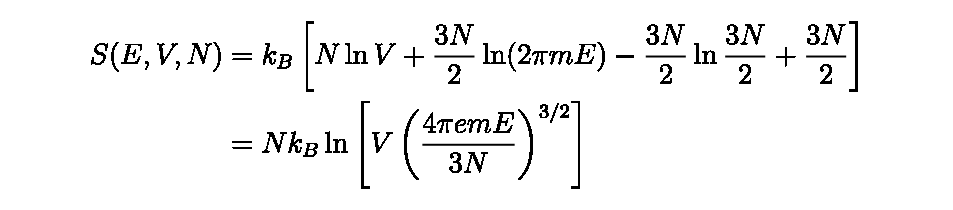

```mathematica
MaTeX["\\begin{aligned}S(E, V, N) & =k_{B}\\left[N \\ln V+\\frac{3 N}{2} \\ln (2 \\pi m E)-\\frac{3 N}{2} \\ln \\frac{3 N}{2}+\\frac{3 N}{2}\\right] \\\\& =N k_{B} \\ln \\left[V\\left(\\frac{4 \\pi e m E}{3 N}\\right)^{3 / 2}\\right]\\end{aligned}", Magnification -> 4]
```

(18) -- In our exploration of ideal gases, we can derive their key properties from a fundamental thermodynamic equation:

TdS = dE + PdV - μdN

This equation connects changes in entropy (S) with changes in energy (E), volume (V), and the number of particles (N). Temperature (T), pressure (P), and chemical potential (μ) also play crucial roles. By understanding this relationship, we can uncover how ideal gases behave under various conditions, providing a foundation for more complex thermodynamic systems.

Statistical Mechanics
Ramirez (19)

```mathematica
MaTeX["\\frac{1}{T}=\\left.\\frac{\\partial S}{\\partial E}\\right|_{N, V}=\\frac{3}{2} \\frac{N k_{B}}{E}", Magnification -> 4]
```

-Graphics-

```mathematica
(20) -- The internal energy $E=3 N k_{B} T / 2$, is only a function of $T$, and the heat capacity $C_{V}=$ $3 N k_{B} / 2$, is a constant. The equation of state is obtained from
```

Statistical Mechanics
Ramirez (21)

```mathematica
MaTeX["\\frac{P}{T}=\\left.\\frac{\\partial S}{\\partial V}\\right|_{N, E}=\\frac{N k_{B}}{V}, \\quad \\Longrightarrow \\quad P V=N k_{B} T", Magnification -> 4]
```

-Graphics-

(22) -- The unconditional probability of finding a particle of momentum $\vec{p}_{1}$ in the gas can be calculated from the joint PDF in eq.(IV.27), by integrating over all other variables,

Statistical Mechanics
Ramirez (23)

```mathematica
MaTeX["\\begin{aligned}p\\left(\\vec{p}_{1}\\right) & =\\int d^{3} \\vec{q}_{1} \\prod_{i=2}^{N} d^{3} \\vec{q}_{i} d^{3} \\vec{p}_{i} p\\left(\\left\\{\\vec{q}_{i}, \\vec{p}_{i}\\right\\}\\right) \\\\& =\\frac{V \\Omega\\left(E-\\vec{p}_{1}^{2} / 2 m, V, N-1\\right)}{\\Omega(E, V, N)}\\end{aligned}", Magnification -> 4]
```

-Graphics-

(24) -- When we look at a system of particles, we're interested in how energy is distributed among them. Imagine you have a fixed amount of energy to share among N particles. If we know how much kinetic energy one particle has, the rest of the energy has to be divided among the remaining N-1 particles. 

This idea is mathematically expressed in equation (IV.32), which shows how the total energy of the system relates to the energy of individual particles. It's like having a pie and giving one slice to someone - the rest of the pie must be shared among everyone else.

This concept is crucial in understanding how energy is distributed in a system and forms the basis for many thermodynamic and statistical mechanical calculations.

Statistical Mechanics
Ramirez (25)

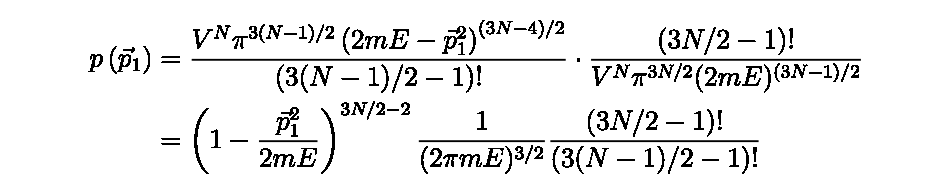

```mathematica
MaTeX["\\begin{aligned}p\\left(\\vec{p}_{1}\\right) & =\\frac{V^{N} \\pi^{3(N-1) / 2}\\left(2 m E-\\vec{p}_{1}^{2}\\right)^{(3 N-4) / 2}}{(3(N-1) / 2-1)!} \\cdot \\frac{(3 N / 2-1)!}{V^{N} \\pi^{3 N / 2}(2 m E)^{(3 N-1) / 2}} \\\\& =\\left(1-\\frac{\\vec{p}_{1}^{2}}{2 m E}\\right)^{3 N / 2-2} \\frac{1}{(2 \\pi m E)^{3 / 2}} \\frac{(3 N / 2-1)!}{(3(N-1) / 2-1)!}\\end{aligned}", Magnification -> 4]
```

```mathematica
(26) -- From Stirling's formula, the ratio of $(3 N / 2-1)$ ! to $(3(N-1) / 2-1)$ ! is approximately $(3 N / 2)^{3 / 2}$, and in the large $E$ limit,
```

Statistical Mechanics
Ramirez (27)

```mathematica
MaTeX["p\\left(\\vec{p}_{1}\\right)=\\left(\\frac{3 N}{4 \\pi m E}\\right)^{3 / 2} \\exp \\left(-\\frac{3 N}{2} \\frac{\\vec{p}_{1}^{2}}{2 m E}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p\\left(\\vec{p}_{1}\\right)=\\left(\\frac{3 N}{4 \\pi m (Ener)}\\right)^{3 / 2} \\exp \\left(-\\frac{3 N}{2} \\frac{\\vec{p}_{1}^{2}}{2 m (Ener)}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[(p⃗)_1]==((3 N)/(4 π m[Ener]))^(3/2) ⅇ^(-((3 N) (p⃗)_1^2)/(2 (2 m[Ener])))

```mathematica
(28) -- Let's look at the Maxwell-Boltzmann distribution in a way that's easier to understand. This distribution shows us how energy is spread out among particles in a system, like gas molecules in a container.

We can simplify the equation by using a special substitution. We replace E with 3NkT/2, where:
- N is the number of particles
- k is Boltzmann's constant
- T is the temperature

This substitution helps us see the relationship between energy and temperature more clearly. It shows that the average energy of the particles is directly related to the temperature of the system.

By using this form, we can more easily predict how particles will behave at different temperatures, which is crucial for understanding many phenomena in thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (29)

```mathematica
MaTeX["p\\left(\\vec{p}_{1}\\right)=\\frac{1}{\\left(2 \\pi m k_{B} T\\right)^{3 / 2}} \\exp \\left(-\\frac{\\vec{p}_{1}^{2}}{2 m k_{B} T}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p\\left(\\vec{p}_{1}\\right)=\\frac{1}{\\left(2 \\pi m k_{B} T\\right)^{3 / 2}} \\exp \\left(-\\frac{\\vec{p}_{1}^{2}}{2 m k_{B} T}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[(p⃗)_1]==(ⅇ^(-((p⃗)_1^2)/(2 m k_B T)))/(2 π m k_B T)^(3/2)

## IV.E Mixing Entropy and Gibbs’ Paradox

```mathematica
(30) -- When we look at the entropy of an ideal gas, we find a problem. The entropy doesn't scale properly when we increase the system size. If we make the energy, volume, and number of particles λ times bigger, the entropy doesn't just become λ times larger. It gets an extra term that depends on λ.

This issue is closely linked to what happens when we mix two gases. Imagine we have two different gases in separate containers at the same temperature. If we remove the barrier between them, they'll mix and spread out to fill the whole space. This mixing can't be undone easily, so the entropy must increase.

The extra entropy that comes from mixing is called the mixing entropy. It's important because it helps us understand how gases behave when they combine, and it reveals some interesting quirks in our understanding of entropy.
```

Statistical Mechanics
Ramirez (31)

```mathematica
MaTeX["\\begin{aligned} S_{i}=S_{1}+S_{2}=\\\\N_{1} k_{B}\\left(\\ln V_{1}+\\sigma_{1}\\right)+N_{2} k_{B}\\left(\\ln V_{2}+\\sigma_{2}\\right) \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S_{i}=S_{1}+S_{2}=N_{1} k_{B}\\left(\\ln V_{1}+\\sigma_{1}\\right)+N_{2} k_{B}\\left(\\ln V_{2}+\\sigma_{2}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S_i==S_1+S_2==N_1 k_B[ln V_1+σ_1]+N_2 k_B[ln V_2+σ_2]

```mathematica
(32) -- where,
```

Statistical Mechanics
Ramirez (33)

```mathematica
MaTeX["\\sigma_{\\alpha}=\\ln \\left(\\frac{4 \\pi e m_{\\alpha}}{3} \\cdot \\frac{E_{\\alpha}}{N_{\\alpha}}\\right)^{3 / 2}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\sigma_{\\alpha}=\\ln \\left(\\frac{4 \\pi e m_{\\alpha}}{3} \\cdot \\frac{(Ener)_{\\alpha}}{N_{\\alpha}}\\right)^{3 / 2}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

σ_α==ln ((4/3 π e m_α)·Ener_α/N_α)^(3/2)

(34) -- is the momentum contribution to the entropy of the $\alpha^{\text {th }}$ gas. Since $E_{\alpha} / N_{\alpha}=3 k_{B} T / 2$ for a monotonic gas,

Statistical Mechanics
Ramirez (35)

```mathematica
MaTeX["\\sigma_{\\alpha}(T)=\\frac{3}{2} \\ln \\left(2 \\pi e m_{\\alpha} k_{B} T\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\sigma_{\\alpha}(T)=\\frac{3}{2} \\ln \\left(2 \\pi e m_{\\alpha} k_{B} T\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

σ_α[T]==3/2 Log[2 π e m_α k_B T]

(36) -- The temperature of the gas is unchanged by mixing, since

Statistical Mechanics
Ramirez (37)

```mathematica
MaTeX["\\frac{3}{2} k_{B} T_{f}=\\frac{E_{1}+E_{2}}{N_{1}+N_{2}}=\\frac{E_{1}}{N_{1}}=\\frac{E_{2}}{N_{2}}=\\frac{3}{2} k_{B} T", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{3}{2} k_{B} T_{f}=\\frac{(Ener)_{1}+(Ener)_{2}}{N_{1}+N_{2}}=\\frac{(Ener)_{1}}{N_{1}}=\\frac{(Ener)_{2}}{N_{2}}=\\frac{3}{2} k_{B} T",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(3 k_B T_f)/2==(Ener_1+Ener_2)/(N_1+N_2)==Ener_1/N_1==Ener_2/N_2==(3 k_B T)/2

```mathematica
(38) -- The final entropy of the mixed gas is
```

Statistical Mechanics
Ramirez (39)

```mathematica
MaTeX["S_{f}=N_{1} k_{B} \\ln \\left(V_{1}+V_{2}\\right)+N_{2} k_{B} \\ln \\left(V_{1}+V_{2}\\right)+k_{B}\\left(N_{1} \\sigma_{1}+N_{2} \\sigma_{2}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S_{f}=N_{1} k_{B} \\ln \\left(V_{1}+V_{2}\\right)+N_{2} k_{B} \\ln \\left(V_{1}+V_{2}\\right)+k_{B}\\left(N_{1} \\sigma_{1}+N_{2} \\sigma_{2}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S_f==N_1 k_B Log[V_1+V_2]+N_2 k_B Log[V_1+V_2]+k_B[N_1 σ_1+N_2 σ_2]

(40) -- There is no change in the contribution from the momenta which depends only on temperature. The mixing entropy,

Statistical Mechanics
Ramirez (41)

```mathematica
MaTeX["\\Delta S_{\\mathrm{Mix}}=S_{f}-S_{i}=N_{1} k_{B} \\ln \\frac{V}{V_{1}}+N_{2} k_{B} \\ln \\frac{V}{V_{2}}=-N k_{B}\\left[\\frac{N_{1}}{N} \\ln \\frac{V_{1}}{V}+\\frac{N_{2}}{N} \\ln \\frac{V_{2}}{V}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Delta S_{\\mathrm{Mix}}=S_{f}-S_{i}=N_{1} k_{B} \\ln \\frac{V}{V_{1}}+N_{2} k_{B} \\ln \\frac{V}{V_{2}}=-N k_{B}\\left[\\frac{N_{1}}{N} \\ln \\frac{V_{1}}{V}+\\frac{N_{2}}{N} \\ln \\frac{V_{2}}{V}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Δ S_Mix==S_f-S_i==(N_1 k_B ln V)/V_1+(N_2 k_B ln V)/V_2==-N k_B[(N_1 ln V_1)/(N V)+(N_2 ln V_2)/(N V)]

```mathematica
(42) -- When we mix different components together, the entropy of the system changes. This change in entropy is due to the new arrangement of molecules in the combined volume. For a simple two-component mixture, we can express this entropy change as:

ΔS_Mix = -Nk_B [(N_1/N)ln(V_1/V) + (N_2/N)ln(V_2/V)]

Here, N is the total number of particles, k_B is Boltzmann's constant, N_1 and N_2 are the numbers of particles of each component, and V_1, V_2, and V are the initial volumes of each component and the final mixed volume.

For mixtures with more than two components, we can extend this formula to:

ΔS_Mix = -Nk_B Σ(N_α/N)ln(V_α/V)

Where the sum is taken over all components α. This equation captures the entropy change solely due to the mixing process, independent of any other factors like temperature or pressure changes.
```

(43) -- Gibbs' Paradox arises when we consider two identical gases separated by a partition. Both gases have the same density, n = N₁/V₁ = N₂/V₂. Intuitively, removing or inserting the partition shouldn't change the system's entropy since the gases are identical. However, our equation for entropy of mixing suggests there should be a change.

To resolve this paradox, we must consider that while the system returns to its initial state after removing and reinserting the partition, the individual particles have moved. Since the particles are identical, we can't distinguish between these configurations. In essence, exchanging identical particles doesn't create new, distinguishable states.

(45) -- a similar exchange has no effect on identical particles, as in

```mathematica
(47) -- Therefore, we have over-counted the phase space associated with $N$ identical particles by the number of possible permutations. As there are $N$ ! permutations leading to indistinguishable micro-states, eq.(IV.32) should be corrected to
```

Statistical Mechanics
Ramirez (48)

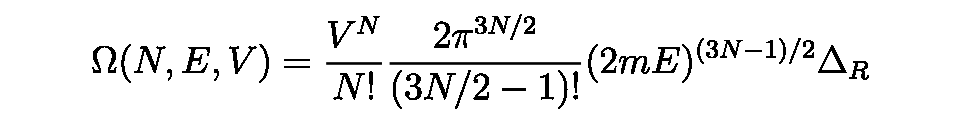

```mathematica
MaTeX["\\Omega(N, E, V)=\\frac{V^{N}}{N!} \\frac{2 \\pi^{3 N / 2}}{(3 N / 2-1)!}(2 m E)^{(3 N-1) / 2} \\Delta_{R}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\Omega(N, Ener, V)=\\frac{V^{N}}{N!} \\frac{2 \\pi^{3 N / 2}}{(3 N / 2-1)!}(2 m (Ener))^{(3 N-1) / 2} \\Delta_{R}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Ω[N,Ener,V]==(V^N (2 π^((3 N)/2)) (2 m[Ener])^(1/2 (3 N-1)) Δ_R)/(N! ((3 N)/2-1)!)

```mathematica
(49) -- resulting in a modified entropy,
```

Statistical Mechanics
Ramirez (50)

```mathematica
MaTeX["\\begin{aligned} S=k_{B} \\ln \\Omega\\\\ =k_{B}[N \\ln V-N \\ln N+N \\ln e]+N k_{B} \\sigma=\\\\N k_{B}\\left[\\ln \\frac{e V}{N}+\\sigma\\right] \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S=k_{B} \\ln \\Omega=k_{B}[N \\ln V-N \\ln N+N \\ln e]+N k_{B} \\sigma=N k_{B}\\left[\\ln \\frac{e V}{N}+\\sigma\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S==k_B ln Ω==k_B[N ln V-N ln N+N ln e]+N k_B σ==N k_B[(ln eV)/N+σ]

```mathematica
(51) -- As the argument of the logarithm has changed from $V$ to $V / N$, the final expression is now properly extensive. The mixing entropies can be recalculated using eq.(IV.47). For the mixing of distinct gases,
```

Statistical Mechanics
Ramirez (52)

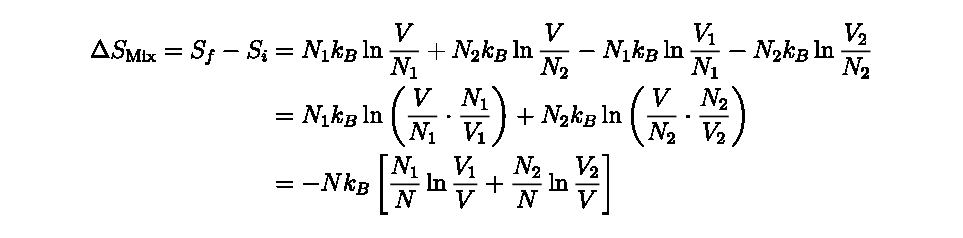

```mathematica
MaTeX["\\begin{aligned}\\Delta S_{\\mathrm{Mix}}=S_{f}-S_{i} & =N_{1} k_{B} \\ln \\frac{V}{N_{1}}+N_{2} k_{B} \\ln \\frac{V}{N_{2}}-N_{1} k_{B} \\ln \\frac{V_{1}}{N_{1}}-N_{2} k_{B} \\ln \\frac{V_{2}}{N_{2}} \\\\& =N_{1} k_{B} \\ln \\left(\\frac{V}{N_{1}} \\cdot \\frac{N_{1}}{V_{1}}\\right)+N_{2} k_{B} \\ln \\left(\\frac{V}{N_{2}} \\cdot \\frac{N_{2}}{V_{2}}\\right) \\\\& =-N k_{B}\\left[\\frac{N_{1}}{N} \\ln \\frac{V_{1}}{V}+\\frac{N_{2}}{N} \\ln \\frac{V_{2}}{V}\\right]\\end{aligned}", Magnification -> 4]
```

(53) -- When we mix two identical gases, something interesting happens. Imagine we have two containers of the same gas, each with its own number of particles and volume. We'll call the first container's particle count N₁ and volume V₁, and the second container's N₂ and V₂.

Now, here's the key point: The ratio of particles to volume is the same in both containers before mixing. We can write this as:

N₁/V₁ = N₂/V₂

When we mix these gases, the total number of particles becomes N₁ + N₂, and the total volume becomes V₁ + V₂. Interestingly, the ratio of total particles to total volume after mixing is exactly the same as it was for each container before mixing:

(N₁ + N₂)/(V₁ + V₂) = N₁/V₁ = N₂/V₂

This relationship is crucial for understanding how identical gases behave when mixed under these specific conditions.

Statistical Mechanics
Ramirez (54)

```mathematica
MaTeX["\\begin{aligned} \\Delta S_{\\mathrm{Mix}}=S_{f}-S_{i}=\\left(N_{1}+N_{2}\\right) k_{B} \\ln \\frac{V_{1}+V_{2}}{N_{1}+N_{2}}-N_{1} k_{B} \\ln \\frac{V_{1}}{N_{1}}-N_{2} k_{B} \\ln \\frac{V_{2}}{N_{2}}=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Delta S_{\\mathrm{Mix}}=S_{f}-S_{i}=\\left(N_{1}+N_{2}\\right) k_{B} \\ln \\frac{V_{1}+V_{2}}{N_{1}+N_{2}}-N_{1} k_{B} \\ln \\frac{V_{1}}{N_{1}}-N_{2} k_{B} \\ln \\frac{V_{2}}{N_{2}}=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Δ S_Mix==S_f-S_i==((N_1+N_2) k_B ln (V_1+V_2))/(N_1+N_2)-(N_1 k_B ln V_1)/N_1-(N_2 k_B ln V_2)/N_2==0

(55) -- When we consider the final state of a system with particles, we need to account for how they can be arranged. For distinct particles, the available volume is V^(N₁+N₂) divided by N₁!N₂!. This takes into account the different ways we can arrange N₁ particles of one type and N₂ particles of another type. However, if all the particles are identical, the available volume becomes V^(N₁+N₂) divided by (N₁+N₂)!. This difference arises because identical particles are indistinguishable, reducing the number of unique arrangements.

## Additional comments on the microcanonical entropy

(57) -- Let's consider our two-level impurities in a solid matrix. Unlike particles in a gas, these impurities are fixed in place. Each impurity has its own unique position in the solid, making them distinguishable from one another. Because of this, we don't need to include the N! factor in our calculations. This N! factor is typically used for indistinguishable particles to account for different arrangements. But here, since each impurity has a specific location, we can tell them apart. This simplifies our statistical treatment of the system.

```mathematica
(58) -- When we fixed the equation for ideal gas entropy, it didn't change how we calculate energy and pressure. This is good news because it means our previous work on those calculations is still valid.

The main reason we needed to correct the entropy formula was to make sure the chemical potential behaves correctly. Specifically, we want the chemical potential to be intensive. This means it shouldn't change if we increase the size of the system while keeping the concentration the same.

Remember, in thermodynamics, intensive properties (like temperature or pressure) don't depend on the amount of material, while extensive properties (like volume or total energy) do. Getting this right for chemical potential is crucial for understanding how substances behave in various situations.
```

Statistical Mechanics
Ramirez (60)

```mathematica
MaTeX["\\begin{aligned} \\frac{\\mu}{T}=-\\left.\\frac{\\partial S}{\\partial N}\\right|_{E, V}=-\\frac{S}{N}+\\frac{5}{2} k_{B}=\\\\ k_{B} \\ln \\left[\\frac{V}{N}\\left(\\frac{4 \\pi m E}{3 N}\\right)^{3 / 2}\\right] \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(61) -- In classical mechanics, we run into a bit of a problem when dealing with identical particles. Imagine you're trying to track a bunch of identical marbles on a computer. The computer can easily tell which marble is which, even if you swap them around. But in reality, if two particles are truly identical, there's no way to tell them apart after they've been swapped.

This is where quantum mechanics comes to the rescue! In the quantum world, identical particles are described by special wave functions that naturally account for this indistinguishability. When we count the possible arrangements of these particles, we automatically get a factor of N! (N factorial) popping up in our calculations. This N! factor is crucial for correctly counting the number of microstates in statistical mechanics.

So, while classical mechanics struggles with the concept of truly identical particles, quantum mechanics handles it beautifully, giving us a more accurate picture of how these particles behave in large numbers.
```

(62) --   \item Yet another difficulty with the expression (IV.47), resolved in quantum statistical mechanics, is the arbitrary constant that appears in changing the units of measurement for $q$ and $p$. The volume of phase space involves products $p q$, of coordinates and conjugate momenta, and hence has dimensions of (action) ${ }^{N}$. Quantum mechanics provides the appropriate measure of action in Planck's constant $h$. Anticipating these quantum results, we shall henceforth set the measure of phase space for identical particles to(62) -- Let's talk about a tricky part of classical statistical mechanics. When we look at the phase space of a system, we run into a problem with units. The volume of phase space is measured by multiplying position (q) and momentum (p) for each particle. This gives us units of "action" raised to the power of N, where N is the number of particles.

Now, here's the issue: we don't have a natural unit for action in classical physics. This means we could change our units for q and p, and it would change our results in a way that doesn't make physical sense.

Luckily, quantum mechanics comes to our rescue! It gives us a natural unit of action called Planck's constant, which we represent with the letter h. This constant helps us measure phase space in a consistent way.

So, to fix this problem in our classical calculations, we're going to borrow this idea from quantum mechanics. From now on, when we deal with identical particles, we'll use Planck's constant to measure our phase space volume. This way, our results will make more sense and be more in line with what we observe in nature.

```mathematica
(63) -- \end{enumerate}(63) -- Here's a simplified version of the text, written as if for an undergraduate thermodynamics textbook:

3. The Boltzmann factor e^(-βE) plays a crucial role in determining the probability of a system being in a particular state with energy E at a given temperature. Here, β = 1/(kT), where k is the Boltzmann constant and T is the absolute temperature.

4. The partition function Z is the sum of all possible Boltzmann factors for a system. It's a key concept in statistical mechanics, helping us calculate various thermodynamic properties.

5. For a system with discrete energy levels, the partition function is calculated by summing the Boltzmann factors for each energy level:

   Z = Σ e^(-βEᵢ)

   where Eᵢ represents the energy of the i-th state.

6. In systems with continuous energy levels, we use an integral instead of a sum to calculate the partition function:

   Z = ∫ e^(-βE) ρ(E) dE

   where ρ(E) is the density of states at energy E.
```

Statistical Mechanics
Ramirez (64)

```mathematica
MaTeX["d \\Gamma_{N}=\\frac{1}{h^{3 N} N!} \\prod_{i=1}^{N} d^{3} \\vec{q}_{i} d^{3} \\vec{p}_{i}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d \\Gamma_{N}=\\frac{1}{h^{3 N} N!} \\prod_{i=1}^{N} d^{3} \\vec{q}_{i} d^{3} \\vec{p}_{i}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d Γ_N==(∏_(i=1)^N d^3 (q⃗)_i d^3 (p⃗)_i)/(h^(3 N) N!)

## IV.F The Canonical Ensemble

```mathematica
(65) -- Let's talk about something cool in thermodynamics called the canonical ensemble. 

In our earlier discussions, we looked at systems where we knew the exact energy, and we figured out the temperature from that. But guess what? We can flip this around!

Instead of starting with a fixed energy, we can start with a fixed temperature. This is what we call the canonical ensemble. Here's how it works:

We have our system S at a constant temperature T. It's in contact with a big heat reservoir R. This reservoir is so huge that its temperature doesn't change when it interacts with our system.

Now, the neat thing is that our system S can exchange heat with the reservoir, but it can't do any work. We describe the state of our system using T and some other parameters x.

To find out how likely different microscopic states μ are, we consider the whole setup (S + R) as one big microcanonical ensemble. The total energy E_Tot is much bigger than the energy of our system E_S.

This approach lets us calculate probabilities for different microscopic states of our system S, even though we started by fixing the temperature instead of the energy. Pretty cool, right?
```

Statistical Mechanics
Ramirez (66)

```mathematica
MaTeX["\\begin{aligned} p\\left(\\mu_{\\mathrm{S}} \\otimes \\mu_{\\mathrm{R}}\\right)=\\\\ \\frac{1}{\\Omega_{\\mathrm{S} \\oplus \\mathrm{R}}\\left(E_{\\mathrm{Tot}}\\right)} \\cdot \\begin{cases}1 & \\text {for} \\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right)+\\mathcal{H}_{\\mathrm{R}}\\left(\\mu_{\\mathrm{R}}\\right)=E_{\\mathrm{Tot}} \\\\ 0 & \\text {otherwise}\\end{cases} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(67) -- The unconditional probability for micro-states of $\mathrm{S}$ is now obtained from
```

Statistical Mechanics
Ramirez (68)

```mathematica
MaTeX["p\\left(\\mu_{\\mathrm{S}}\\right)=\\sum_{\\left\\{\\mu_{\\mathrm{R}}\\right\\}} p\\left(\\mu_{\\mathrm{S}} \\otimes \\mu_{\\mathrm{R}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p\\left(\\mu_{\\mathrm{S}}\\right)=\\sum_{\\left\\{\\mu_{\\mathrm{R}}\\right\\}} p\\left(\\mu_{\\mathrm{S}} \\otimes \\mu_{\\mathrm{R}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[μ_S]==Sum[p[μ_S⊗μ_R],{μ_R}]

(69) -- When we set a specific value for μS (the state of our system), we're essentially fixing the energy of our system. This means the remaining energy in the total setup must be in the reservoir. 

The number of ways the reservoir can arrange itself with this leftover energy is directly related to its entropy. This is a key concept in statistical mechanics.

By counting these possible arrangements, we can determine how likely our system is to be in the state μS. This probability is crucial for understanding the behavior of the system as a whole.

Statistical Mechanics
Ramirez (70)

```mathematica
MaTeX["\\begin{aligned} p\\left(\\mu_{\\mathrm{S}}\\right)=\\frac{\\Omega_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}-\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right)\\right)}{\\Omega_{\\mathrm{S} \\oplus \\mathrm{R}}\\left(E_{\\mathrm{Tot}}\\right)} \\propto \\\\ \\exp \\left[\\frac{1}{k_{B}} S_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}-\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right)\\right)\\right] \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p\\left(\\mu_{\\mathrm{S}}\\right)=\\frac{\\Omega_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}-\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right)\\right)}{\\Omega_{\\mathrm{S} \\oplus \\mathrm{R}}\\left(E_{\\mathrm{Tot}}\\right)} \\propto \\exp \\left[\\frac{1}{k_{B}} S_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}-\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right)\\right)\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(p[μ_S]==Ω_R[ⅇ_Tot-HermiteH[S,μ_S]]/(Ω_(S⊕R)[ⅇ_Tot]))∝exp[S_R[ⅇ_Tot-HermiteH[S,μ_S]]/k_B]

```mathematica
(71) -- In our system, we consider the energy to be very small compared to the massive reservoir it's connected to. Think of it like a tiny drop of water in a vast ocean. The ocean's total energy barely changes when we add or remove that drop. This assumption allows us to simplify our calculations and focus on the behavior of our small system without worrying about significant changes in the reservoir.
```

Statistical Mechanics
Ramirez (72)

```mathematica
MaTeX["\\begin{aligned} S_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}-\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right)\\right) \\approx \\\\ S_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}\\right)-\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right) \\frac{\\partial S_{\\mathrm{R}}}{\\partial E_{\\mathrm{R}}}=S_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}\\right)-\\frac{\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right)}{T} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}-\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right)\\right) \\approx S_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}\\right)-\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right) \\frac{\\partial S_{\\mathrm{R}}}{\\partial E_{\\mathrm{R}}}=S_{\\mathrm{R}}\\left(E_{\\mathrm{Tot}}\\right)-\\frac{\\mathcal{H}_{\\mathrm{S}}\\left(\\mu_{\\mathrm{S}}\\right)}{T}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(S_R[ⅇ_Tot-HermiteH[S,μ_S]]≈S_R[ⅇ_Tot]-HermiteH[S,μ_S] ∂_{ⅇ_R} S_R)==S_R[ⅇ_Tot]-HermiteH[S,μ_S]/T

```mathematica
(73) -- Dropping the subscript S, the normalized probabilities are given by
```

Statistical Mechanics
Ramirez (74)

```mathematica
MaTeX["p_{(T, \\mathbf{x})}(\\mu)=\\frac{e^{-\\beta} \\mathcal{H}(\\mu)}{Z(T, \\mathbf{x})}", Magnification -> 4]
```

-Graphics-

```mathematica
(75) -- The normalization
```

Statistical Mechanics
Ramirez (76)

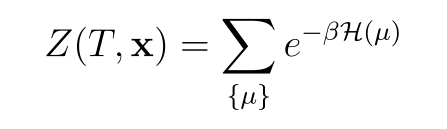

```mathematica
MaTeX["Z(T, \\mathbf{x})=\\sum_{\\{\\mu\\}} e^{-\\beta \\mathcal{H}(\\mu)}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["Z(T, \\mathbf{x})=\\sum_{\\{\\mu\\}} e^{-\\beta \\mathcal{H}(\\mu)}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Z[T,x]==Sum[e^(-β H[μ]),{μ}]

```mathematica
(77) -- In thermodynamics and statistical mechanics, we often use a special function called the partition function. It's represented by Z and helps us understand how energy is distributed in a system. 

We also use β, which is equal to 1 divided by (kB times T), where kB is Boltzmann's constant and T is temperature. This β helps us relate energy to temperature.

Remember, we've seen similar probability expressions before when we looked at parts of a system in balance with the rest. These ideas help us understand how energy and probability are connected in thermodynamic systems.
```

```mathematica
(78) -- Let's think about the internal energy E of our system S. In a microcanonical ensemble, we know the exact energy, but when our system can exchange heat with its surroundings, things get more interesting. The energy isn't fixed anymore; it becomes a variable that can change.

We can describe this changing energy using a probability distribution, which we call p(E). To find this distribution, we start with the probability distribution of the system's microstates, p(μ), and then we switch from thinking about microstates to thinking about energies. We do this by replacing μ with H(μ), where H is the Hamiltonian function that gives us the energy of each microstate.

This approach helps us understand how the energy of our system behaves when it's in contact with a heat reservoir, even though we can't pin down an exact value for the energy at any given moment.
```

Statistical Mechanics
Ramirez (79)

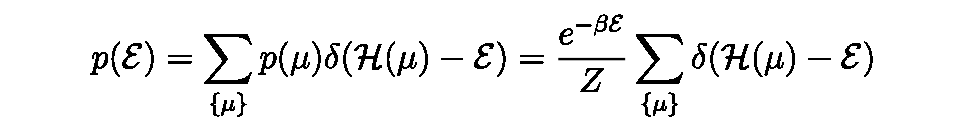

```mathematica
MaTeX["p(\\mathcal{E})=\\sum_{\\{\\mu\\}} p(\\mu) \\delta(\\mathcal{H}(\\mu)-\\mathcal{E})=\\frac{e^{-\\beta \\mathcal{E}}}{Z} \\sum_{\\{\\mu\\}} \\delta(\\mathcal{H}(\\mu)-\\mathcal{E})", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["p(\\mathcal{E})=\\sum_{\\{\\mu\\}} p(\\mu) \\delta(\\mathcal{H}(\\mu)-\\mathcal{E})=\\frac{e^{-\\beta \\mathcal{E}}}{Z} \\sum_{\\{\\mu\\}} \\delta(\\mathcal{H}(\\mu)-\\mathcal{E})",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[ⅇ]==Sum[p[μ] δ[H[μ]-ⅇ],{μ}]==(e^(-β ⅇ) Sum[δ[H[μ]-ⅇ],{μ}])/Z

```mathematica
(80) -- In thermodynamics, we're often interested in counting the number of ways a system can arrange itself while having a specific energy. This count is represented by Ω(E), where E is the energy of the system. Ω(E) tells us how many different microscopic configurations, or microstates, are available to the system at that energy. This concept is fundamental to understanding the relationship between the microscopic world of atoms and molecules and the macroscopic properties we observe in everyday life.
```

Statistical Mechanics
Ramirez (81)

```mathematica
MaTeX["\\begin{aligned} p(\\mathcal{E})=\\frac{\\Omega(\\mathcal{E}) e^{-\\beta \\mathcal{E}}}{Z}=\\\\ \\frac{1}{Z} \\exp \\left[\\frac{S(\\mathcal{E})}{k_{B}}-\\frac{\\mathcal{E}}{k_{B} T}\\right]=\\frac{1}{Z} \\exp \\left[-\\frac{F(\\mathcal{E})}{k_{B} T}\\right] \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p(\\mathcal{E})=\\frac{\\Omega(\\mathcal{E}) e^{-\\beta \\mathcal{E}}}{Z}=\\frac{1}{Z} \\exp \\left[\\frac{S(\\mathcal{E})}{k_{B}}-\\frac{\\mathcal{E}}{k_{B} T}\\right]=\\frac{1}{Z} \\exp \\left[-\\frac{F(\\mathcal{E})}{k_{B} T}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[ⅇ]==(Ω[ⅇ] e^(-β ⅇ))/Z==exp[S[ⅇ]/k_B-ⅇ/(k_B T)]/Z==exp[-F[ⅇ]/(k_B T)]/Z

(82) -- We've defined F as E - TS(E). This F is related to what we call the Helmholtz free energy in thermodynamics. 

Now, when we look at the probability p(E), we find it has a sharp peak at a specific energy, which we call E*. This E* is special because it makes F(E) as small as possible.

To understand this better, we can use a technique we learned earlier about adding up exponentials. This helps us see why E* is so important and how it relates to the system's behavior.

By thinking about energy this way, we can predict how a system will behave without needing to know all the tiny details about its particles.

Statistical Mechanics
Ramirez (83)

```mathematica
MaTeX["Z=\\sum_{\\{\\mu\\}} e^{-\\beta \\mathcal{H}(\\mu)}=\\sum_{\\mathcal{E}} e^{-\\beta F(\\mathcal{E})} \\approx e^{-\\beta F\\left(E^{*}\\right)}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["Z=\\sum_{\\{\\mu\\}} e^{-\\beta \\mathcal{H}(\\mu)}=\\sum_{\\mathcal{E}} e^{-\\beta F(\\mathcal{E})} \\approx e^{-\\beta F\\left(E^{*}\\right)}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(Z==Sum[e^(-β H[μ]),{μ}]==∑_ⅇ e^(-β F[ⅇ]))≈e^(-β F[ⅇ^*])

(84) -- The average energy computed from the distribution in eq.(IV.59) is

Statistical Mechanics
Ramirez (85)

```mathematica
MaTeX["\\begin{aligned} \\langle\\mathcal{H}\\rangle=\\sum_{\\mu} \\mathcal{H}(\\mu) \\frac{e^{-\\beta} \\mathcal{H}(\\mu)}{Z}=\\\\ -\\frac{1}{Z} \\frac{\\partial}{\\partial \\beta} \\sum_{\\mu} e^{-\\beta \\mathcal{H}}=-\\frac{\\partial \\ln Z}{\\partial \\beta} \\end{aligned}", Magnification -> 4]
```

-Graphics-

(86) -- In our study of thermodynamics, we previously came across a comparable formula for energy. You might remember it as equation (I.37). This energy equation shares some similarities with what we're discussing now. Think of it as a cousin to our current topic – related, but not identical. Understanding these connections helps us build a more complete picture of how energy behaves in thermodynamic systems.

Statistical Mechanics
Ramirez (87)

```mathematica
MaTeX["\\begin{aligned} E=F+T S=F-\\left.T \\frac{\\partial F}{\\partial T}\\right|_{\\mathbf{x}}=\\\\ -T^{2} \\frac{\\partial}{\\partial T}\\left(\\frac{F}{T}\\right)=\\frac{\\partial(\\beta F)}{\\partial \\beta} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(88) -- Eqs.(IV.60) and (IV.61), both suggest identifying
```

Statistical Mechanics
Ramirez (89)

```mathematica
MaTeX["F(T, \\mathbf{x})=-k_{B} T \\ln Z(T, \\mathbf{x})", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["F(T, \\mathbf{x})=-k_{B} T \\ln Z(T, \\mathbf{x})",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

F[T,x]==-k_B T ln Z[T,x]

```mathematica
(90) -- Let's consider two important energy values: the most likely energy and the average energy. These are given by different equations, but how close are they to each other?

To understand this, we need to look at how spread out the energy values are. We can do this by calculating something called the variance, which tells us about the width of the energy probability distribution.

The variance is related to the average of the energy squared, written as ⟨H.b2⟩c. We can find this easily by using the partition function Z(β), which is connected to the energy distribution. Here, β is related to temperature and plays a role similar to ik in probability theory.

By examining the variance, we can get a sense of how much the energy typically deviates from its average value, and thus how close the most likely energy is to the average energy.
```

Statistical Mechanics
Ramirez (91)

```mathematica
MaTeX["-\\frac{\\partial Z}{\\partial \\beta}=\\sum_{\\mu} \\mathcal{H} e^{-\\beta \\mathcal{H}}, \\quad \\text {and} \\quad \\frac{\\partial^{2} Z}{\\partial \\beta^{2}}=\\sum_{\\mu} \\mathcal{H}^{2} e^{-\\beta \\mathcal{H}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["-\\frac{\\partial Z}{\\partial \\beta}=\\sum_{\\mu} \\mathcal{H} e^{-\\beta \\mathcal{H}};; \\quad \\text {and} \\quad \\frac{\\partial^{2} Z}{\\partial \\beta^{2}}=\\sum_{\\mu} \\mathcal{H}^{2} e^{-\\beta \\mathcal{H}}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{-∂_{β} Z==∑_μ H e^(-β H),and ∂_{β,2} Z==∑_μ H^2 e^(-β H)}

(92) -- In thermodynamics and statistical mechanics, we often work with a function called the partition function, denoted as Z(β). The natural logarithm of this function, ln Z(β), is particularly useful because it generates the cumulants of the system's Hamiltonian, H. 

Cumulants are statistical measures that provide information about the distribution of energy states in our system. By taking derivatives of ln Z(β) with respect to β (which is related to temperature), we can obtain these cumulants, giving us valuable insights into the system's thermal properties and behavior.

This relationship between ln Z(β) and the cumulants of H is a powerful tool in statistical mechanics, allowing us to connect microscopic properties to macroscopic observables.

Statistical Mechanics
Ramirez (93)

```mathematica
MaTeX["\\langle\\mathcal{H}\\rangle_{c}=\\frac{1}{Z} \\sum_{\\mu} \\mathcal{H} e^{-\\beta \\mathcal{H}}=-\\frac{1}{Z} \\frac{\\partial Z}{\\partial \\beta}=-\\frac{\\partial \\ln Z}{\\partial \\beta}", Magnification -> 4]
```

-Graphics-

```mathematica
(94) -- and
```

Statistical Mechanics
Ramirez (95)

```mathematica
MaTeX["\\begin{aligned} \\left\\langle\\mathcal{H}^{2}\\right\\rangle_{c}=\\left\\langle\\mathcal{H}^{2}\\right\\rangle-\\langle\\mathcal{H}\\rangle^{2}=\\\\ \\frac{1}{Z} \\sum_{\\mu} \\mathcal{H}^{2} e^{-\\beta \\mathcal{H}}-\\frac{1}{Z^{2}}\\left(\\sum_{\\mu} \\mathcal{H} e^{-\\beta \\mathcal{H}}\\right)^{2}=\\frac{\\partial^{2} \\ln Z}{\\partial \\beta^{2}}=-\\frac{\\partial\\langle\\mathcal{H}\\rangle}{\\partial \\beta} \\end{aligned}", Magnification -> 4]
```

-Graphics-

(96) -- Imagine you have a bunch of energy values for a system, and you want to describe how they're spread out. The nth cumulant is a special number that helps us do this. It's like a more advanced version of averages and gives us important information about the energy distribution. For example, the first cumulant is just the average energy, while the second cumulant tells us about how much the energy values spread out from that average. Higher cumulants give us even more detailed information about the shape of the energy distribution. This concept is super useful in thermodynamics and statistical mechanics when we're trying to understand how energy behaves in complex systems.

Statistical Mechanics
Ramirez (97)

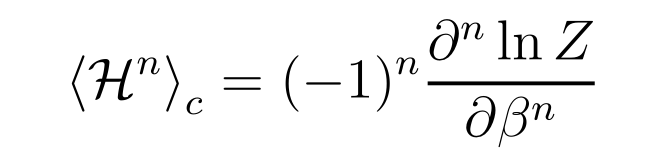

```mathematica
MaTeX["\\left\\langle\\mathcal{H}^{n}\\right\\rangle_{c}=(-1)^{n} \\frac{\\partial^{n} \\ln Z}{\\partial \\beta^{n}}", Magnification -> 4]
```

```mathematica
(98) -- From eq.(IV.66)
```

Statistical Mechanics
Ramirez (99)

```mathematica
MaTeX["\\begin{aligned} \\left\\langle\\mathcal{H}^{2}\\right\\rangle_{c}= -\\frac{\\partial\\langle\\mathcal{H}\\rangle}{\\partial\\left(1 / k_{B} T\\right)}=\\\\ \\left.k_{B} T^{2} \\frac{\\partial\\langle\\mathcal{H}\\rangle}{\\partial T}\\right|_{\\mathbf{x}}, \\quad \\Rightarrow \\quad\\left\\langle\\mathcal{H}^{2}\\right\\rangle_{c}=k_{B} T^{2} C_{\\mathbf{x}} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(100) -- where we have identified the heat capacity with the thermal derivative of the average energy $\langle\mathcal{H}\rangle$. Eq.(IV.68) shows that it is justified to treat the mean and most likely energies interchangeably, since the width of the distribution $p(\mathcal{E})$, only grows as $\sqrt{\left\langle\mathcal{H}^{2}\right\rangle_{c}} \propto N^{1 / 2}$. The relative error, $\sqrt{\left\langle\mathcal{H}^{2}\right\rangle_{c}} /\langle\mathcal{H}\rangle_{c}$ vanishes in the thermodynamic limit as $1 / \sqrt{N}$. (In fact eq.(IV.67) shows that all cumulants of $\mathcal{H}$ are proportional to $N$.) The PDF for energy in a canonical ensemble can thus be approximated by
```

Statistical Mechanics
Ramirez (101)

```mathematica
MaTeX["\\begin{aligned} p(\\mathcal{E})=\\frac{1}{Z} e^{-\\beta F(\\mathcal{E})} \\approx \\\\ \\exp \\left(-\\frac{(\\mathcal{E}-\\langle\\mathcal{H}\\rangle)^{2}}{2 k_{B} T^{2} C_{\\mathbf{x}}}\\right) \\frac{1}{\\sqrt{2 \\pi k_{B} T^{2} C_{\\mathbf{x}}}} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p(\\mathcal{E})=\\frac{1}{Z} e^{-\\beta F(\\mathcal{E})} \\approx \\exp \\left(-\\frac{(\\mathcal{E}-\\langle\\mathcal{H}\\rangle)^{2}}{2 k_{B} T^{2} C_{\\mathbf{x}}}\\right) \\frac{1}{\\sqrt{2 \\pi k_{B} T^{2} C_{\\mathbf{x}}}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(p[ⅇ]==e^(-β F[ⅇ])/Z)≈(ⅇ^(-(ⅇ-⟨H⟩)^2/(2 k_B T^2 C_x)))/(√(2 π k_B T^2 C_x))

```mathematica
(102) -- In large systems, the energy distribution becomes very narrow, allowing us to define a clear internal energy for a canonical ensemble. However, we need to be careful when dealing with systems near certain phase transitions, where the heat capacity C_x can become infinite. This situation requires special consideration, as it can affect how we interpret and calculate thermodynamic properties.
```

(103) -- In our study of thermodynamics, we often use something called canonical probabilities. These probabilities help us understand how likely different energy states are in a system. We find these probabilities by making sure the average energy of the system stays constant.

The cool thing is, we can use these probabilities to calculate the entropy of the canonical ensemble. Entropy is a measure of disorder in a system. To do this calculation, we use a special equation that relates probability to entropy.

By using these methods, we can get a clearer picture of how energy and disorder are distributed in various systems. This is super helpful for understanding everything from gases to complex materials!

Statistical Mechanics
Ramirez (104)

```mathematica
MaTeX["\\begin{aligned} S=-k_{B}\\langle\\ln p(\\mu)\\rangle=\\\\ -k_{B}\\langle(-\\beta \\mathcal{H}-\\ln Z)\\rangle=\\frac{E-F}{T} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S=-k_{B}\\langle\\ln p(\\mu)\\rangle=-k_{B}\\langle(-\\beta \\mathcal{H}-\\ln Z)\\rangle=\\frac{Ener-F}{T}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S==-k_B ⟨ln p[μ]⟩==-k_B ⟨-β H-ln Z⟩==(Ener-F)/T

(105) -- In our earlier discussion, we saw that ln Z is related to free energy. Now, when we look at small systems, the probabilities in the canonical ensemble (where temperature is fixed) are different from those in the microcanonical ensemble (where energy is fixed).

But here's the interesting part: when we consider really large systems (imagine a system with an enormous number of particles), something fascinating happens. The probabilities in the canonical ensemble become very concentrated around the average energy. In fact, they become so focused that they're practically the same as the probabilities in the microcanonical ensemble at that energy level.

This idea of considering extremely large systems is what we call the "thermodynamic limit." It's when we imagine the number of particles (N) becoming infinitely large.

To sum up, while small systems show differences between these two ways of looking at things (canonical and microcanonical), these differences essentially disappear for very large systems.

(106) -- We're looking at two important ensembles: microcanonical and canonical.

In the microcanonical ensemble, we focus on systems with fixed energy (E) and other parameters (x). The probability of finding a specific microstate (μ) is related to the Dirac delta function and the number of available microstates (Ω). The entropy (S) is linked to Ω through Boltzmann's constant (kB).

For the canonical ensemble, we deal with systems at a fixed temperature (T) and parameters (x). Here, the probability of a microstate depends on its energy and the partition function (Z). The Helmholtz free energy (F) is connected to Z and temperature.

These ensembles help us understand how microscopic properties relate to macroscopic observables in thermodynamic systems. Pretty neat, right?

(107) -- In our study of thermodynamics, we encounter two important ensembles: the canonical and microcanonical. Let's compare them:

Canonical Ensemble:
- System can exchange energy with a heat bath
- Temperature T is fixed
- Energy E fluctuates
- Probability of a microstate: P ∝ e^(-E/kT)

Microcanonical Ensemble:
- Isolated system with fixed energy E
- Temperature T is not defined
- All accessible microstates are equally probable
- Probability of a microstate: P = constant (if accessible)

These ensembles help us understand the behavior of systems under different conditions, providing valuable insights into thermodynamic properties.

## Reference

https://assets.cambridge.org/97805218/73420/frontmatter/9780521873420_frontmatter.pdf

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear